## This is for the IRF computed on belief level (01/2024)

```mathematica
(* show naive solution for β = 0 *)
M = .;
β = .;
eChange = pβplus/(2M)(  bjp - bibjp + bic - bibjc   ) - pβminus/(2M) ( bip - bibjp + bjc - bibjc );
FullSimplify[eChange]

eChange = 1/(4M)(  bjp - bibjp + bic - bibjc   ) - 1/(4M) ( bip - bibjp + bjc - bibjc );
FullSimplify[eChange]
```

1/(2 M)((-1+bic) bjc pβminus+bip (-1+bjp) pβminus-bic bjc pβplus-bip bjp pβplus+pβplus (bic+bjp-σc-σp)+pβminus (σc+σp))

(bic-bip-bjc+bjp)/(4 M)

Tanh[(o β)/2]

1/(1+ⅇ^(-o β))

0

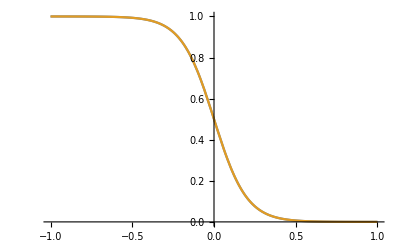

```mathematica
(* two nice properties of the exponential form *)
pβ[o_,m_,β_]:= 1/(1+Exp[-β o m]);
FullSimplify[pβ[o,1,β]-pβ[o,-1,β]]

pβ[o,1,β]
FullSimplify[pβ[o,1,β]-(1-pβ[o,-1,β])]

Plot[{1-pβ[o,1,10],pβ[o,-1,10]},{o,-1,1}]
```

```mathematica
(* full model before covariance trick *)
bibjp =.;
bibjc = .;
eChange = pβ[o,1,β]/(2M)(  bjp - bibjp + bic - bibjc   ) - pβ[o,-1,β]/(2M) ( bip - bibjp + bjc - bibjc )
FullSimplify[eChange]
```

(-bibjc-bibjp+bic+bjp)/(2 (1+ⅇ^(-4 o)) M)-(-bibjc-bibjp+bip+bjc)/(2 (1+ⅇ^(4 o)) M)

(bibjc+bibjp-bip-bjc+(-bibjc-bibjp+bic+bjp) ⅇ^(4 o))/(2 (1+ⅇ^(4 o)) M)

```mathematica
(* covariance trick *)
bibjp = bip bjp +σp
bibjc = bic bjc +σc
oi = .;
oj = .;

eChange = pβ[oi,1,β]/(2M)(  bjp - bibjp + bic - bibjc   ) - pβ[oi,-1,β]/(2M) ( bip - bibjp + bjc - bibjc )
FullSimplify[eChange]
```

bip bjp+σp

bic bjc+σc

-(bip+bjc-bic bjc-bip bjp-σc-σp)/(2 (1+ⅇ^(oi β)) M)+(bic-bic bjc+bjp-bip bjp-σc-σp)/(2 (1+ⅇ^(-oi β)) M)

((-1+bic) bjc+bip (-1+bjp)+σc+σp-ⅇ^(oi β) (bic (-1+bjc)+(-1+bip) bjp+σc+σp))/(2 (1+ⅇ^(oi β)) M)

#### .... from here on I am trying to find a good form ....

```mathematica
(* Putting in the naive solution *)

oi = .;
oj =.;
naive = 1/(4M)(oj-oi  + (1-oi oj)Tanh[oi β / 2]  )
Expand[naive]

oi = bip-bic;
oj = bjp-bjc;

eChange = pβ[oi,1,β]/(2M)(  bjp - bibjp + bic - bibjc   ) - pβ[oi,-1,β]/(2M) ( bip - bibjp + bjc - bibjc );

rest = FullSimplify[eChange-naive]
(*Expand[rest]*)
```

(-oi+oj+(1-oi oj) Tanh[(oi β)/2])/(4 M)

-oi/(4 M)+oj/(4 M)+Tanh[(oi β)/2]/(4 M)-(oi oj Tanh[(oi β)/2])/(4 M)

((1-bjc-bjp+bic (-1+bjc+bjp)+bip (-1+bjc+bjp)+2 σc+2 σp) Tanh[1/2 (bic-bip) β])/(4 M)

```mathematica
Expand[(1-bjc-bjp+bic (-1+bjc+bjp)+bip (-1+bjc+bjp)+2 σc+2 σp)]
```

1-bic-bip-bjc+bic bjc+bip bjc-bjp+bic bjp+bip bjp+2 σc+2 σp

```mathematica
e01 = FullSimplify[rest+naive]
FullSimplify[eChange-e01]
```

1/(4 M)(bic-bip-bjc+bjp+(1-bip-bjc+bic (-1+2 bjc)-bjp+2 bip bjp+2 σc+2 σp) Tanh[1/2 (bic-bip) β]+Tanh[1/2 (-bic+bip) β])

0

0

2 Tanh[(a β)/2]

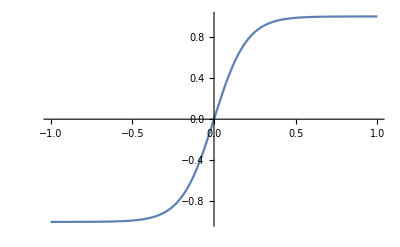

```mathematica
(* Properties of Tanh *)
Tanh[1/2 a β]+Tanh[-1/2 a β]
Tanh[1/2 a β]-Tanh[-1/2 a β]
Plot[Tanh[ 10 o / 2],{o,-1,1}]
```

```mathematica
Expand[(1-bip-bjc+bic (-1+2 bjc)-bjp+2 bip bjp+2 σc+2 σp)]
```

```mathematica
1-bic-bip-bjc-bjp+2 bic bjc+2 bip bjp+2 σc+2 σp
```

1-bic-bip-bjc+2 bic bjc-bjp+2 bip bjp+2 σc+2 σp

```mathematica
Expand[oi oj]
Expand[(1-bic-bip-bjc-bjp+2 bic bjc+2 bip bjp+2 σc+2 σp)]
Expand[oi oj - (1-bic-bip-bjc-bjp+2 bic bjc+2 bip bjp+2 σc+2 σp)]
```

bic bjc-bip bjc-bic bjp+bip bjp

1-bic-bip-bjc+2 bic bjc-bjp+2 bip bjp+2 σc+2 σp

-1+bic+bip+bjc-bic bjc-bip bjc+bjp-bic bjp-bip bjp-2 σc-2 σp

```mathematica
(* Test *)
```

```mathematica
x = 1-bic-bip-bjc+2 bic bjc-bjp+2 bip bjp+2 σc+2 σp
xnaive = oi oj
naive =(bic-bip-bjc+bjp + Tanh[1/2 (-bic+bip) β]-xnaive Tanh[1/2 (-bic+bip) β])/(4 M)
exact= (bic-bip-bjc+bjp + Tanh[1/2 (-bic+bip) β]-x Tanh[1/2 (-bic+bip) β])/(4 M)
FullSimplify[eChange-exact]
```

1-bic-bip-bjc+2 bic bjc-bjp+2 bip bjp+2 σc+2 σp

(-bic+bip) (-bjc+bjp)

(bic-bip-bjc+bjp+Tanh[1/2 (-bic+bip) β]-(-bic+bip) (-bjc+bjp) Tanh[1/2 (-bic+bip) β])/(4 M)

1/(4 M)(bic-bip-bjc+bjp+Tanh[1/2 (-bic+bip) β]-(1-bic-bip-bjc+2 bic bjc-bjp+2 bip bjp+2 σc+2 σp) Tanh[1/2 (-bic+bip) β])

0

4

4

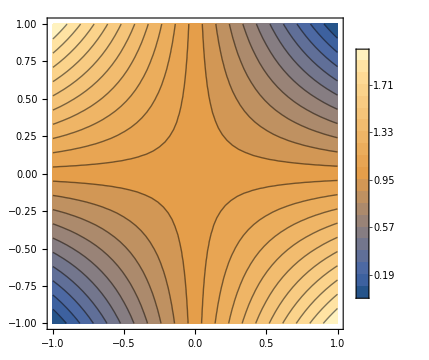

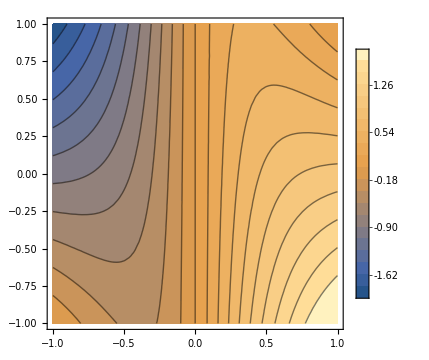

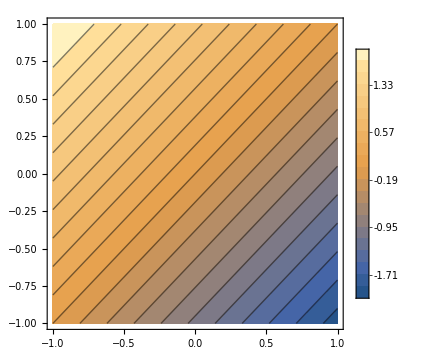

```mathematica
M = 4
β = 4
g1 =ContourPlot[(1-oi oj),{oi,-1,1},{oj,-1,1},PlotLegends->Automatic,Contours->20,(*ColorFunction->(If[#<0,Directive[Lighter[Blue,1-4M Abs[#]]],Directive[Lighter[Red,1-4M Abs[#]]]]&),ColorFunctionScaling->False,*)ImageSize->Medium]
g2 =ContourPlot[(1-oi oj)Tanh[oi β/2],{oi,-1,1},{oj,-1,1},PlotLegends->Automatic,Contours->20,(*ColorFunction->(If[#<0,Directive[Lighter[Blue,1-4M Abs[#]]],Directive[Lighter[Red,1-4M Abs[#]]]]&),ColorFunctionScaling->False,*)ImageSize->Medium]
g3 =ContourPlot[ oj-oi,{oi,-1,1},{oj,-1,1},PlotLegends->Automatic,Contours->20,(*ColorFunction->(If[#<0,Directive[Lighter[Blue,1-4M Abs[#]]],Directive[Lighter[Red,1-4M Abs[#]]]]&),ColorFunctionScaling->False,*)ImageSize->Medium]
```

#### ... hier hab ich versucht noch einmal nach o_i und o_j aufzulösen, aber das führt nicht wirklich weiter ...

```mathematica
e03 = 1/(4 M)(oj-oi+(1-bip-bjc+bic (-1+2 bjc)-bjp+2 bip bjp+2 σc+2 σp) Tanh[-1/2 oi β]+Tanh[1/2 oi β])
FullSimplify[eChange-e03]
```

1/(4 M)(bic-bip-bjc+bjp+Tanh[1/2 (-bic+bip) β]-(1-bip-bjc+bic (-1+2 bjc)-bjp+2 bip bjp+2 σc+2 σp) Tanh[1/2 (-bic+bip) β])

0

-2 Tanh[(a β)/2]

```mathematica
r01 = FullSimplify[(1-oi-oj+2(bip+bjp+ bip bjp+bic bjc+ σc+ σp))-(1-bip-bjc+bic (-1+2 bjc)-bjp+2 bip bjp+2 σc+2 σp) ]

FullSimplify[(1-oi-oj+2(bip+bjp+ bip bjp+bic bjc+ σc+ σp-bic-bip-bjc-bjp))-(1-bip-bjc+bic (-1+2 bjc)-bjp+2 bip bjp+2 σc+2 σp) ]

Expand[(1-oi-oj+2(bip+bjp+ bip bjp+bic bjc+ σc+ σp-bic-bip-bjc-bjp))]
```

2 (bic+bip+bjc+bjp)

0

1-bic-bip-bjc+2 bic bjc-bjp+2 bip bjp+2 σc+2 σp

```mathematica
e04 = 1/(4 M)(oj-oi+(1-oi-oj+2(bip+bjp+ bip bjp+bic bjc+ σc+ σp)) Tanh[-1/2 oi β]+Tanh[1/2 oi β])
FullSimplify[eChange-e04]
```

1/(4 M)(bic-bip-bjc+bjp+Tanh[1/2 (-bic+bip) β]-(1+bic-bip+bjc-bjp+2 (bip+bic bjc+bjp+bip bjp+σc+σp)) Tanh[1/2 (-bic+bip) β])

-((bic+bip+bjc+bjp) Tanh[1/2 (bic-bip) β])/(2 M)

## This is the naive approach not computed on belief level (06/2022)

(1-oj)/2

(1+oj)/2

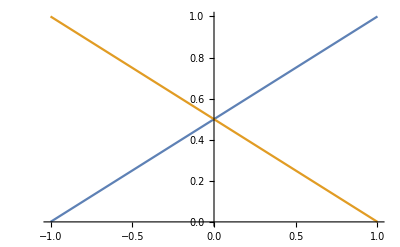

```mathematica
ClearAll["Global`*"]
β = .;
pMPlus[oj_]:= (1+oj)/(2);
pMMinus[oj_]:= (1-oj)/(2); 
FullSimplify[pMMinus[oj]]
FullSimplify[pMPlus[oj]]
Plot[{pMPlus[oj],pMMinus[oj]},{oj,-1,1}]
```

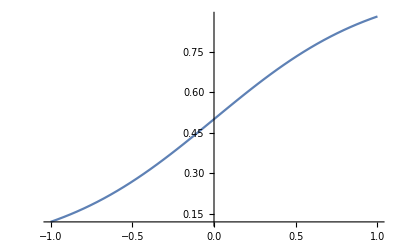

```mathematica
β = 2;
Plot[1/(1+Exp[-β oi]),{oi,-1,1}]
```

-(-1+oi)/(2 (1+ⅇ^(-oi β)))

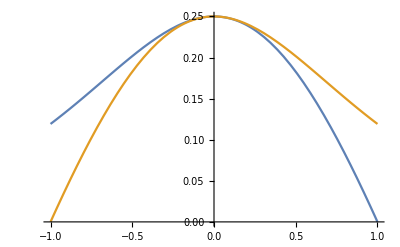

```mathematica
β = .;
pNewPlus[oi_]:= (1-oi)/(2);
pNewMinus[oi_]:= (1+oi)/(2);
pAcceptPlus[oi_]:= pNewPlus[oi]  * 1/(1+Exp[-β oi])
pAcceptMinus[oi_]:= pNewMinus[oi]  * 1/(1+Exp[β oi])
FullSimplify[pAcceptPlus[oi]]
β = 2;
Plot[{pAcceptPlus[oi],pAcceptMinus[oi]},{oi,-1,1}]
β=.;
```

```mathematica
M = .;
β = .;
oj=.;
oi=.;
pDeltaPlus[oi_,oj_]:= pAcceptPlus[oi]*pMPlus[oj]
pDeltaMinus[oi_,oj_]:= pAcceptMinus[oi]*pMMinus[oj]
eChange[oi_,oj_]:= 1/(M) (pDeltaPlus[oi,oj] - pDeltaMinus[oi,oj])

FullSimplify[pDeltaPlus[oi,oj]]
eChange[oi,oj]
FullSimplify[eChange[oi,oj]]
```

((1-oi) (1+oj))/(4 (1+ⅇ^(-oi β)))

(-((1+oi) (1-oj))/(4 (1+ⅇ^(oi β)))+((1-oi) (1+oj))/(4 (1+ⅇ^(-oi β))))/M

(-oi+oj+(1-oi oj) Tanh[(oi β)/2])/(4 M)

4

4

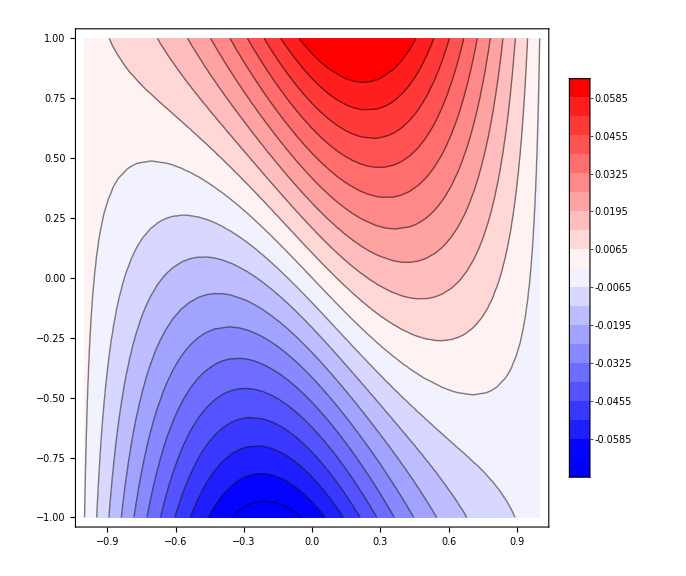

```mathematica
M = 4
β = 4
g1 =ContourPlot[eChange[oi,oj],{oi,-1,1},{oj,-1,1},PlotLegends->Automatic,Contours->20,ColorFunction->(If[#<0,Directive[Lighter[Blue,1-4M Abs[#]]],Directive[Lighter[Red,1-4M Abs[#]]]]&),ColorFunctionScaling->False,ImageSize->Large]
```

```mathematica
eChange[0.25,-0.5]
```

-0.0143824

## What kind of approximation is this?

```mathematica
FullSimplify[  oj - npi npj - nci ncj - σ1 - σ2 -((1+oj)(1-oi)), {oi == npi-nci,oj == npj-ncj}    ]
FullSimplify[  npj - npj npi + nci-nci ncj -σ -((1+oj)(1-oi)), {oi == npi-nci,oj == npj-ncj}    ]
FullSimplify[  npj - npj npi + nci-nci ncj -σ , {oi == npi-nci,oj == npj-ncj}    ]
```

-1+oi+npj oi+npi (-2 npj+oj)-σ1-σ2

-1+npj+npj oi-oj+npi (1-2 npj+oj)-σ

nci-nci ncj+npj-npi npj-σ

```mathematica
b1 = {1,0,0,1,1,0,0,1};
b2 = {1,0,1,1,1,1,1,1};
Covariance[b1,b2]//N
Mean[b1*b2]-Mean[b1]*Mean[b2]//N
```

0.0714286

0.0625

```mathematica
β=.;
pAdoptPlus[oi_]:=1/(1+Exp[-β oi]);
pAdoptMinus[oi_]:=1/(1+Exp[β oi]);

FullSimplify[1/(2M)(npj +nci - x1)pAdoptPlus[npi-nci] -1/(M) (npi+ncj - x2)pAdoptMinus[npi-nci],{oi == npi-nci,oj == npj-ncj}]

FullSimplify[1/(2M)(npj +nci - x1) pAdoptPlus[npi-nci] -1/(M) (npi+ncj - x2)pAdoptMinus[npi-nci]]
```

(ⅇ^(oi β) (npi+npj-oi-x1)-2 (ncj+npi-x2))/(2 (1+ⅇ^(oi β)) M)

(ⅇ^((-nci+npi) β) (nci+npj-x1)-2 (ncj+npi-x2))/(2 (1+ⅇ^((-nci+npi) β)) M)

```mathematica
Delta := (oj -oi -npj-nci+ⅇ^(oi β) (nci+npj-x1)+x2)/(2 (1+ⅇ^(oi β)) M)
```

```mathematica
β =0;
FullSimplify[1/(2M)(npj +nci - x1)pAdoptPlus[npi-nci] -1/(2M) (npi+ncj - x2)pAdoptMinus[npi-nci] - eChange[oi,oj],{oi == npi-nci,oj == npj-ncj}]
FullSimplify[ eChange[oi,oj]]
FullSimplify[1/(2M)(npj +nci - x1)pAdoptPlus[npi-nci] -1/(2M) (npi+ncj - x2)pAdoptMinus[npi-nci],{oi == npi-nci,oj == npj-ncj}]
```

(-x1+x2)/(4 M)

(-oi+oj)/(4 M)

(-oi+oj-x1+x2)/(4 M)

## This is the first succesfull trail but there are still some tiny issues with the rescaling of opinions to [-1,1]

```mathematica
M=.;
pMPlus[oj_]:= (oj+M)/(2M);

pMMinus[oj_]:= 1-(oj+M)/(2M); 

FullSimplify[pMMinus[oj]]
FullSimplify[pMPlus[oj]]
```

(M-oj)/(2 M)

(M+oj)/(2 M)

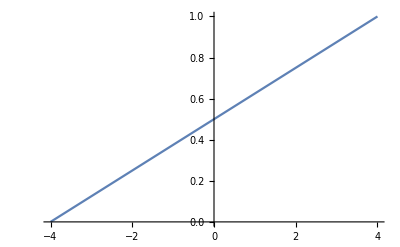

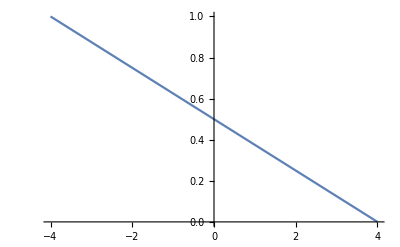

```mathematica
M = 4;
Plot[pMPlus[oj],{oj,-4,4}]
Plot[pMMinus[oj],{oj,-4,4}]
```

```mathematica
pAcceptPlus[oi_]:= pMMinus[oi]  * 1/(1+Exp[-β oi])
pAcceptMinus[oi_]:= pMPlus[oi]  * 1/(1+Exp[β oi])
FullSimplify[pAcceptPlus[oi]]
```

-1/16 (-4+oi) (1+Tanh[2 oi])

```mathematica
FullSimplify[1/(1+Exp[-β oi m] )-Exp[β oi m]/(1+Exp[β oi m] )]
```

0

4

0.4

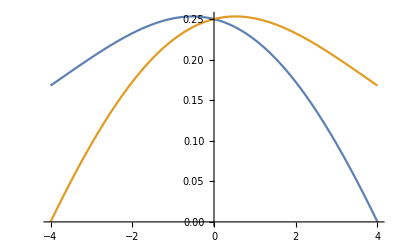

```mathematica
M = 4
β = 0.4
Plot[{pAcceptPlus[oi],pAcceptMinus[oi]},{oi,-M,M}]
```

```mathematica
M = .;
β = .;
pDeltaPlus[oi_,oj_]:= pAcceptPlus[oi]*pMPlus[oj]
pDeltaMinus[oi_,oj_]:= pAcceptMinus[oi]*pMMinus[oj]
eChange[oi_,oj_]:= 1/(M) (pDeltaPlus[oi,oj] - pDeltaMinus[oi,oj])
```

```mathematica
M = .;
FullSimplify[pDeltaPlus[oi,oj]]
FullSimplify[pDeltaPlus[oi,oj]/Tanh[(oi β)/2]]
```

(ⅇ^(oi β) (M-oi) (M+oj))/(4 (1+ⅇ^(oi β)) M^2)

(ⅇ^(oi β) (M-oi) (M+oj))/(4 (-1+ⅇ^(oi β)) M^2)

4

0.5

-1

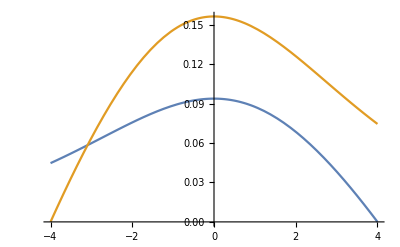

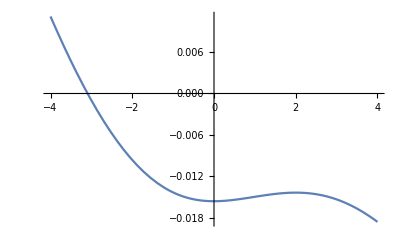

```mathematica
M = 4
β = 0.5
oj=-1
Plot[{pDeltaPlus[oi,oj],pDeltaMinus[oi,oj]},{oi,-M,M}]
Plot[eChange[oi,oj],{oi,-M,M}]
```

```mathematica
4
```

4

4

5.2

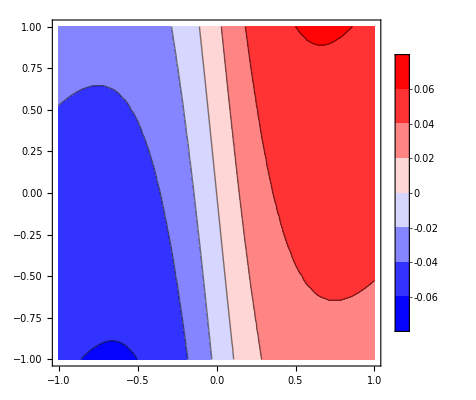

```mathematica
M = 4
β = 5.2
g1 =ContourPlot[eChange[oi,oj],{oi,-1,1},{oj,-1,1},PlotLegends->Automatic,Contours->Automatic,ColorFunction->(If[#<0,Directive[Lighter[Blue,1-4M Abs[#]]],Directive[Lighter[Red,1-4M Abs[#]]]]&),ColorFunctionScaling->False]
```

```mathematica
oj= .;
β = .;
M = 4;
FullSimplify[eChange[oi,oj]]
```

1/16 (-oi+oj)